## Gabriel Patenotte 08.13-08.16

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True];
```

## Na and Cs atom energy levels

Mathematica code to visualize the low energy fine structure of Na 23 and Cs 133. The atomLevels matrices contain the relevant information for plotting and labeling the levels. Their information comes from the online NIST energy level tables. The levelDiagram function takes this information and creates energy level diagrams. The visible E1 transitions are shown with the approximately correct laser color. The arrows button shows/hides the E1 transitions and their respective frequencies.

```mathematica
naLevels=({{"n", "S", "L", "J", "Parity", "Level (cm^(-1))", "graphic"}, {3, 1/2, 0, 1/2, 0, 0, 0}, {3, 1/2, 1, 1/2, 1, 16956.172, -1}, {3, 1/2, 1, 3/2, 1, 16973.368, 1}, {4, 1/2, 0, 1/2, 0, 25739.991, 0}, {4, 1/2, 2, 5/2, 0, 29172.839, -1}, {3, 1/2, 2, 3/2, 0, 29172.889, 1}, {4, 1/2, 1, 1/2, 1, 30266.99, -1}, {4, 1/2, 1, 3/2, 1, 30272.58, 1}});
csLevels=({{"n", "S", "L", "J", "Parity", "Level (cm^(-1))", "graphic"}, {6, 1/2, 0, 1/2, 0, 0, 0}, {6, 1/2, 1, 1/2, 1, 11178.2686, -1}, {6, 1/2, 1, 3/2, 1, 11732.3079, 1}, {5, 1/2, 2, 3/2, 0, 14499.2584, -1}, {5, 1/2, 2, 5/2, 0, 14596.8423, 1}, {7, 1/2, 0, 1/2, 0, 18535.529, 0}, {7, 1/2, 1, 1/2, 1, 21765.35, -1}, {7, 1/2, 1, 3/2, 1, 21946.396, 1}});
```

Replacement rules for the term symbol notation:

```mathematica
ruleL={0->S,1->P,2->D,3->F};
rulePar={0->"",1->°};
```

Term symbol notation. This somewhat complicated use of box functions is to have a superscript in front of an ordinary letter:

```mathematica
term[n_,S_,L_,J_,par_]:=RowBox[{n,SuperscriptBox["",2S+1],SubsuperscriptBox[L/.ruleL,J,par/.rulePar]}]//DisplayForm
```

Energy level diagram function. The energy is rescaled to eV units using the 1 eV: 8065.73 cm^-1 ratio. Some lines are very close in energy. To make some of the labels not overlap, the ‘graphic’ term in the atomLevels matrix shifts around the labels. For some tables, there is an if statement for whether to add an item to be graphed. For instance, one of the if statements checks that only E1 transitions are displayed. In the case that a transition is not E1, the ##&[] else tells mathematica to put a vanishing function, which serves to not add anything to the graphic.

```mathematica
levelDiagram[atom_]:=Manipulate[Graphics[{If[arrows,Table[If[Abs[atom[[j,3]]-atom[[i,3]]]==1,{Text[StringForm["`` nm",10^7/Abs[atom[[j,6]]-atom[[i,6]]]],{1/2(atom[[j,3]]+.25+.25atom[[j,7]]+atom[[i,3]]+.25+.25atom[[i,7]]),(1/8065.73 atom[[j,6]]+1/8065.73 atom[[i,6]])/2+.1atom[[i,7]]+.1atom[[j,7]]}],Arrowheads[{-.02,.02}],ColorData["VisibleSpectrum"][10^7/Abs[atom[[j,6]]-atom[[i,6]]]],Arrow[{{atom[[j,3]]+.25+.25atom[[j,7]],1/8065.73 atom[[j,6]]},{atom[[i,3]]+.25+.25atom[[i,7]],1/8065.73 atom[[i,6]]}}]},##&[]],{i,3,9},{j,2,9}],##&[]],Table[{Thick,Line[{{atom[[i,3]],1/8065.73 atom[[i,6]]},{atom[[i,3]]+.5,1/8065.73 atom[[i,6]]}}],Black,Text[term@@atom[[i,1;;5]],{atom[[i,3]]+.7,1/8065.73 atom[[i,6]]+.1atom[[i,7]]}]},{i,2,9}]},Axes->{False,True},AxesLabel->{"L","Energy (eV)"},PlotRange->{{-.4,3},{-.1,4}},ImageSize->500,AspectRatio->1],{{arrows,False},{True,False}}]
```

```mathematica
{levelDiagram/@{naLevels,csLevels}}[[1]]
```

{,}

## NaCs molecule |c^3 Σ_1, v'=26⟩ level

Will’s simulation for the v=26 state of c^3 Σ_1 NaCs appears to closely predict the observed lines, but is off by some fixed frequency. Based on the linear model below, Will’s numbers at too high by around 0.85 MHz.

The two images are the |c^3 Σ_1, v'=26⟩ spectroscopy from the 2021 molecule paper, and Will’s theory from the NaCs 1.5 2021 notebook.

```mathematica
-Graphics--Graphics--Graphics-
```

The two lists below are the transition frequencies adjacent to the pump transition frequency. The ‘the’ory comes from Will’s tables, and the ‘exp’eriment comes from my guesswork of where the survival dips are located (not precise!)

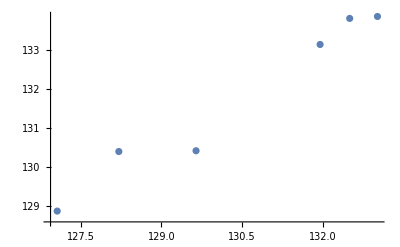

```mathematica
exp=130+{-2.935,-1.79,-.355,1.95,2.5,3.016};
the={128.86,130.39,130.41,133.14,133.81,133.86};
ListPlot[Transpose@{exp,the}]
```

```mathematica
lm=LinearModelFit[Transpose@{exp,the},x,x]
```

FittedModel[20.8819+0.850193 x]

## 3-level Hamiltonian (practice)

```mathematica
Clear[H3,Ωs,Ωp];
Ωs=PS 10^6 Piecewise[{{1 -Sqrt[((t- t1)/w )^2 + 0.01],Abs[t -t1]<w}},0];
Ωp= PP 10^6 Piecewise[{{1 -Sqrt[((t- 30 10^-6)/w )^2 + 0.01],Abs[t -30 10^-6]<w}},0];
Δp=DO +DP 10^6 Piecewise[{{ (t- 30 10^-6-t2p)/w,Abs[t -30 10^-6-t2p]<w}},0];
Δs=DO+DS 10^6 Piecewise[{{ (t- 30 10^-6-t2s)/w,Abs[t -30 10^-6-t2s]<w}},0];
```

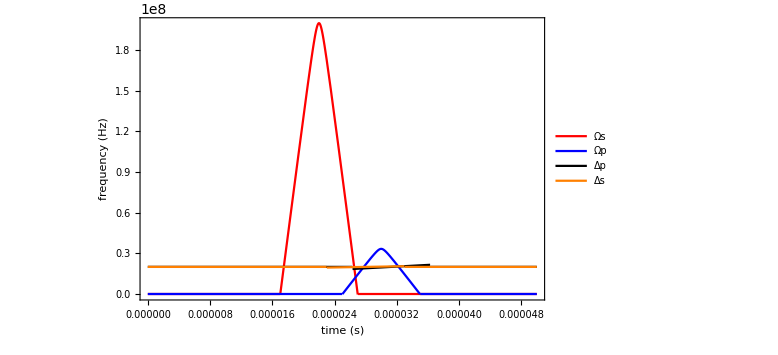

```mathematica
Plot[Evaluate
[{Ωs,Ωp,Δp,Δs}/.{t1->22 10^-6,w-> 5 10^-6,PS->222,PP-> 37,DP->1.55,DS->.5,DO->20 10^6,t2p->1.3 10^-6,t2s->-2 10^-6}],{t,0,50 10^-6},ImageSize->Large,PlotRange->All,FrameLabel->{"time (s)","frequency (Hz)"},PlotLegends->{"Ωs","Ωp","Δp","Δs"}]
```

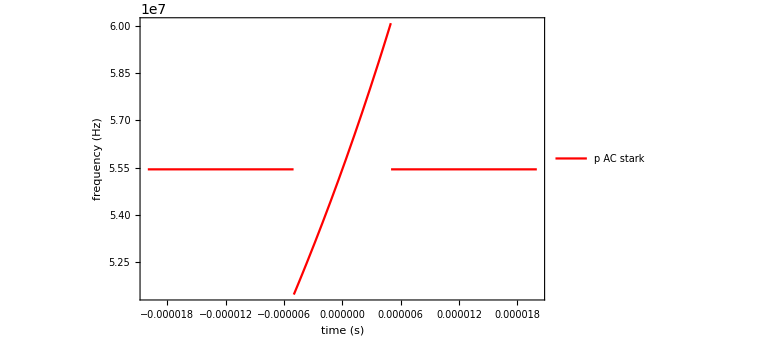

```mathematica
Plot[Evaluate
[{Ωp^2/Δp}/.{t1->22 10^-6,w-> 5 10^-6,PS->222,PP-> 37,DP->1.55,DS->.5,DO->20 10^6,t-> 30 10^-6,t2s->-2 10^-6}],{t2p,-20 10^-6,20 10^-6},ImageSize->Large,PlotRange->All,FrameLabel->{"time (s)","frequency (Hz)"},PlotLegends->{"p AC stark"}]
```

```mathematica
P[t_]={p1[t],p2[t],p3[t],p4[t]};
init=P[0]=={1,0,0,0};
H[t_]=2π({{0, 1/2 0.1897/0.1897 Ωp, 1/2(1.7432+0.67256)/0.1897 Ωp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2(1.7432+0.67256)/0.1897 Ωp, 0, Δp+(133.86-130.41)10^9-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, Δp-Δs}});
SE=ⅈ P'[t]==H[t].P[t];
PSoln=ParametricNDSolve[{SE/.Γ->100 10^6,init},{p1,p2,p3,p4},{t,0,100/10^6},{t1,w,PS,PP,DP,DS,DO,t2p,t2s},PrecisionGoal->6];
```

```mathematica
plots[t1_,w_,PS_,PP_,DP_,DS_,DO_,t2p_,t2s_]:=Plot[{Evaluate[Abs[p1[t1,w,PS,PP,DP,DS,DO,t2p,t2s][t]]^2/.PSoln],Evaluate[100 Abs[p2[t1,w,PS,PP,DP,DS,DO,t2p,t2s][t]]^2/.PSoln],Evaluate[100 Abs[p3[t1,w,PS,PP,DP,DS,DO,t2p,t2s][t]]^2/.PSoln],Evaluate[Abs[p4[t1,w,PS,PP,DP,DS,DO,t2p,t2s][t]]^2/.PSoln]},{t,15/10^6,37/10^6},ImageSize->Large,PlotLegends->{"p1","p2","p3","p4"},FrameLabel->{"t [s]",Abs[ψ]^2},PlotRange->All]
```

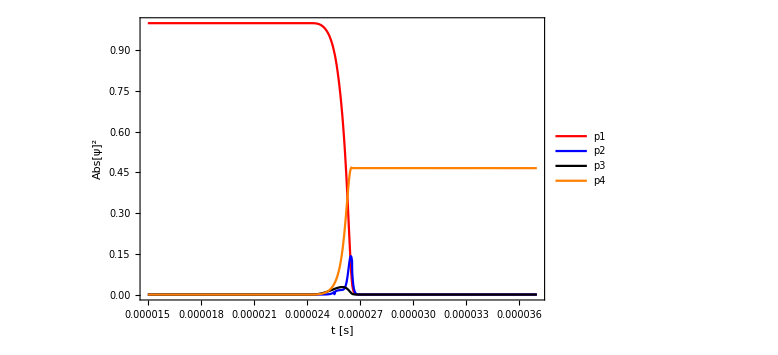
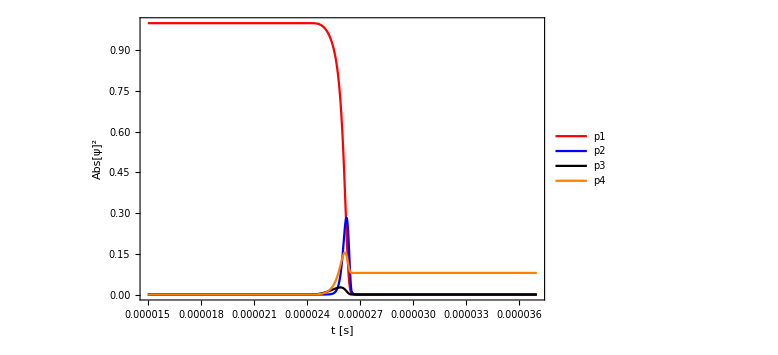

```mathematica
{plots[20.78/10^6,5.77/10^6,222,37,2,0.5,0 10^6,1.3 10^-6,-2 10^-6],plots[20.78/10^6,5.77/10^6,222,37,0,0,0 10^6,0,0]}
```

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.0000257251.

InterpolatingFunction::dmval: Input value {3/100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

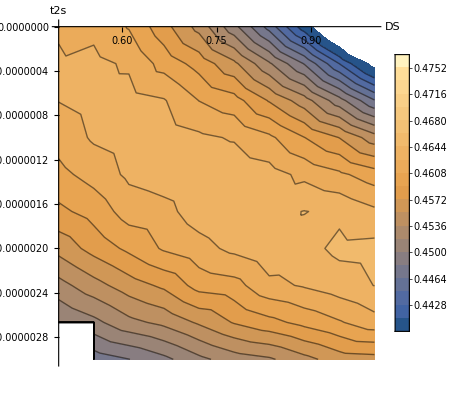

```mathematica
ContourPlot[Evaluate[Abs[p4[20.78/10^6,5.77/10^6,222,37,2.2,DS,0,1.3 10^-6,t2s][30 10^-6]]^2/. PSoln] ,{DS,0.5,1},{t2s,-3 10^-6,0},PlotLegends->Automatic,Axes -> True,Frame->False,Exclusions->None,AxesLabel->{"DS","t2s"}, PerformanceGoal->"Speed", Contours->20]
```

```mathematica
cplot[twoΔ_]:=ContourPlot[Evaluate[Abs[p4[20.78/10^6,5.77/10^6,222,37,DP,DS,twoΔ 10^6][30 10^-6]]^2/. PSoln] ,{DP,-2,4},{DS,-1,1},PlotLegends->Automatic,Axes -> True,Frame->False,Exclusions->None,AxesLabel->{"Pulse time [s]","Pulse width [s]"}, PerformanceGoal->"Speed", Contours->20]
```

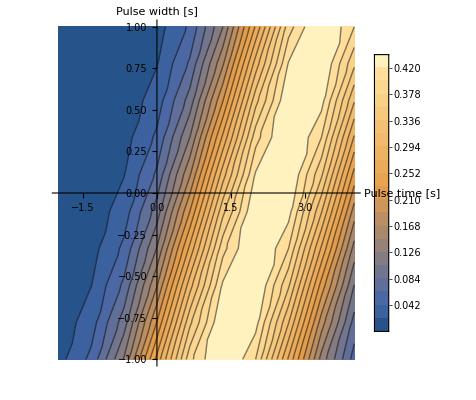
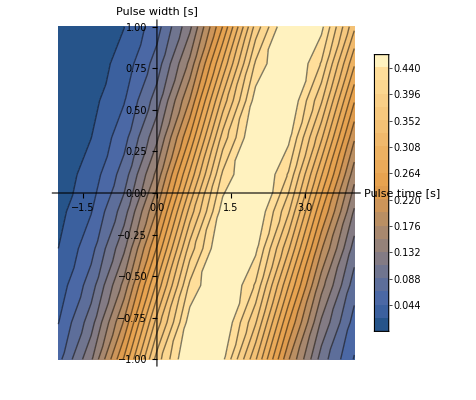
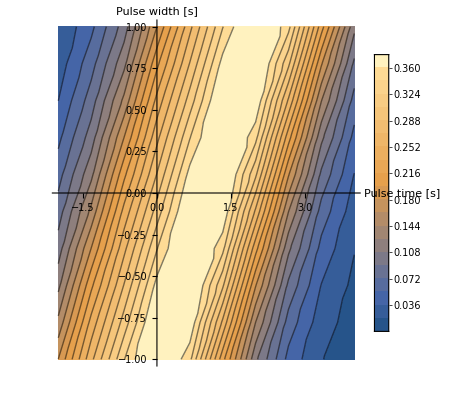

```mathematica
{cplot[0],cplot[50],cplot[200]}
```

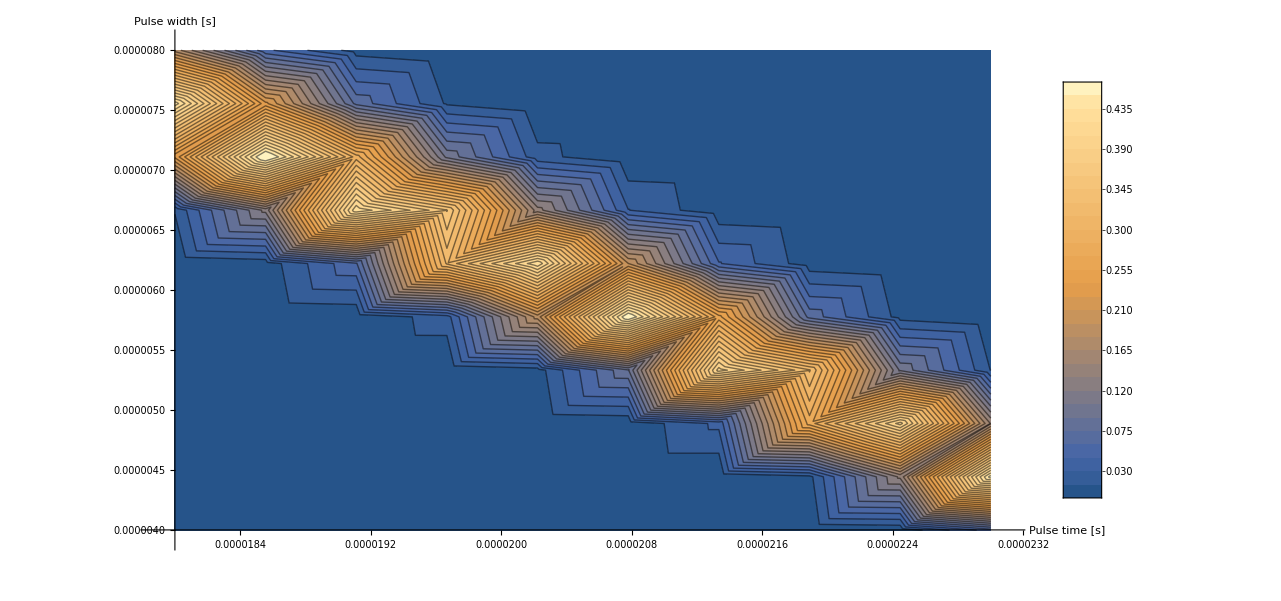

```mathematica
Eigenvalues[({{0, 1/2 Ω}, {1/2 Ω, Δ}})]
```

{1/2 (Δ-√(Δ^2+Ω^2)),1/2 (Δ+√(Δ^2+Ω^2))}